```mathematica
A=RegionPlot3D[x*x+y*y+z*z≤1,{x,-4,4},{y,-4,4},{z,-4,4},Mesh->None,PlotPoints->100,PlotStyle->Directive[Green,Opacity[0.8]],Boxed->False,BoundaryStyle->None,ImageSize->600,Axes->False,PlotRange->{-4,4}];
Needs["NDSolve`FEM`"];
mesh=ToElementMesh[DiscretizeGraphics[A],"MeshOrder"->1];
stressOperator[Y_,ν_]:={Inactive[Div][({{0,0,-((Y ν)/((1-2 ν) (1+ν)))},{0,0,0},{-(Y/(2 (1+ν))),0,0}}.Inactive[Grad][w[x,y,z],{x,y,z}]),{x,y,z}]+Inactive[Div][({{0,-((Y ν)/((1-2 ν) (1+ν))),0},{-(Y/(2 (1+ν))),0,0},{0,0,0}}.Inactive[Grad][v[x,y,z],{x,y,z}]),{x,y,z}]+Inactive[Div][({{-((Y (1-ν))/((1-2 ν) (1+ν))),0,0},{0,-(Y/(2 (1+ν))),0},{0,0,-(Y/(2 (1+ν)))}}.Inactive[Grad][u[x,y,z],{x,y,z}]),{x,y,z}],Inactive[Div][({{0,0,0},{0,0,-((Y ν)/((1-2 ν) (1+ν)))},{0,-(Y/(2 (1+ν))),0}}.Inactive[Grad][w[x,y,z],{x,y,z}]),{x,y,z}]+Inactive[Div][({{0,-(Y/(2 (1+ν))),0},{-((Y ν)/((1-2 ν) (1+ν))),0,0},{0,0,0}}.Inactive[Grad][u[x,y,z],{x,y,z}]),{x,y,z}]+Inactive[Div][({{-(Y/(2 (1+ν))),0,0},{0,-((Y (1-ν))/((1-2 ν) (1+ν))),0},{0,0,-(Y/(2 (1+ν)))}}.Inactive[Grad][v[x,y,z],{x,y,z}]),{x,y,z}],Inactive[Div][({{0,0,0},{0,0,-(Y/(2 (1+ν)))},{0,-((Y ν)/((1-2 ν) (1+ν))),0}}.Inactive[Grad][v[x,y,z],{x,y,z}]),{x,y,z}]+Inactive[Div][({{0,0,-(Y/(2 (1+ν)))},{0,0,0},{-((Y ν)/((1-2 ν) (1+ν))),0,0}}.Inactive[Grad][u[x,y,z],{x,y,z}]),{x,y,z}]+Inactive[Div][({{-(Y/(2 (1+ν))),0,0},{0,-(Y/(2 (1+ν))),0},{0,0,-((Y (1-ν))/((1-2 ν) (1+ν)))}}.Inactive[Grad][w[x,y,z],{x,y,z}]),{x,y,z}]};
h=-0.6;
Subscript[Γ,D]={DirichletCondition[{u[x,y,z]==0.,v[x,y,z]==0.,w[x,y,z]==0.},{z≥h}]};
Subscript[Γ2,D]={DirichletCondition[{u[x,y,z]==0.,v[x,y,z]==0.,w[x,y,z]==-z+h},{z<h}]};
```

```mathematica
E0=10^6;
V0=33/100;
mf=NDSolveValue[{stressOperator[E0,V0]=={0,0,0},Subscript[Γ,D],Subscript[Γ2,D]},{u,v,w},{x,y,z}∈mesh];
test[mf_,x_,y_,z_]:=(
{mf[[1]][x,y,z],mf[[2]][x,y,z],mf[[3]][x,y,z]}
);
uik=(Grad[test[mf,x,y,z],{x,y,z}]+
Transpose[Grad[test[mf,x,y,z],{x,y,z}]])/2.0;
```

```mathematica
ull2=Tr[uik]^2;
uik2=Total[Flatten[uik]*Flatten[uik]];
```

```mathematica
Length[Flatten[uik2]]
```

6

```mathematica
Length[Flatten[uik2]]
```

6

```mathematica
Length[Flatten[Total[Flatten[uik]*Flatten[uik]]]]
```

6

```mathematica
gt=Flatten[uik]*Flatten[uik];
Total[gt]
```

1. (InterpolatingFunction[{{-0.998382, 0.998382}, {-0.998382, 0.998382}, {-0.998382, 0.998382}}, <>][x,y,z])^2+1. (InterpolatingFunction[{{-0.998382, 0.998382}, {-0.998382, 0.998382}, {-0.998382, 0.998382}}, <>][x,y,z])^2+0.5 (InterpolatingFunction[{{-0.998382, 0.998382}, {-0.998382, 0.998382}, {-0.998382, 0.998382}}, <>][x,y,z]+InterpolatingFunction[{{-0.998382, 0.998382}, {-0.998382, 0.998382}, {-0.998382, 0.998382}}, <>][x,y,z])^2+0.5 (InterpolatingFunction[{{-0.998382, 0.998382}, {-0.998382, 0.998382}, {-0.998382, 0.998382}}, <>][x,y,z]+InterpolatingFunction[{{-0.998382, 0.998382}, {-0.998382, 0.998382}, {-0.998382, 0.998382}}, <>][x,y,z])^2+1. (InterpolatingFunction[{{-0.998382, 0.998382}, {-0.998382, 0.998382}, {-0.998382, 0.998382}}, <>][x,y,z])^2+0.5 (InterpolatingFunction[{{-0.998382, 0.998382}, {-0.998382, 0.998382}, {-0.998382, 0.998382}}, <>][x,y,z]+InterpolatingFunction[{{-0.998382, 0.998382}, {-0.998382, 0.998382}, {-0.998382, 0.998382}}, <>][x,y,z])^2

```mathematica
Fden=E0/(2*(1+V0))*(uik2+V0/(1-2V0)ull2);
F=NIntegrate[Fden,{x,y,z}∈Sphere[{0,0,0},1]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 462775. and 5686.72 for the integral and error estimates.

462775.

```mathematica
Fden=E0/(2*(1+V0))*(uik2+V0/(1-2V0)ull2);
Fden/.x->0./.y->0./.z->0.
```

12222.9

```mathematica
Transpose[({{0.04453046507868109, 0.002096748725536269, 0.005419980109094155}, {0.0000984727787937921, 0.03612840549969844, 0.004744346828925529}, {-0.0024265129408422223, -0.03497400961945352, -0.1536088308346556}})]
```

{{0.0445305,0.0000984728,-0.00242651},{0.00209675,0.0361284,-0.034974},{0.00541998,0.00474435,-0.153609}}

```mathematica
50000000/133 (0.25+33/34 Tr[0.5 (({{0.04453046507868109, 0.002096748725536269, 0.005419980109094155}, {0.0000984727787937921, 0.03612840549969844, 0.004744346828925529}, {-0.0024265129408422223, -0.03497400961945352, -0.1536088308346556}})+Transpose[({{0.04453046507868109, 0.002096748725536269, 0.005419980109094155}, {0.0000984727787937921, 0.03612840549969844, 0.004744346828925529}, {-0.0024265129408422223, -0.03497400961945352, -0.1536088308346556}})])]^2+(({{0.04453046507868109, 0.002096748725536269, 0.005419980109094155}, {0.0000984727787937921, 0.03612840549969844, 0.004744346828925529}, {-0.0024265129408422223, -0.03497400961945352, -0.1536088308346556}})+Transpose[({{0.04453046507868109, 0.002096748725536269, 0.005419980109094155}, {0.0000984727787937921, 0.03612840549969844, 0.004744346828925529}, {-0.0024265129408422223, -0.03497400961945352, -0.1536088308346556}})])^2)
```

{{98908.7,95928.6,95930.1},{95928.6,97889.6,96270.3},{95930.1,96270.3,131409.}}

```mathematica
Tr[]]
```

2

```mathematica
Transpose[{{1,1},{0,1}}]
```

{{1,0},{1,1}}

```mathematica
Length[ull2]
```

2

```mathematica
Length[Total[Flatten[uik]*Flatten[uik]]]
```

6

```mathematica
gt=Flatten[uik]*Flatten[uik];
Length[gt]
Length[Total[gt]]
Length[uik2]
```

9

6

6

```mathematica
gt[[1]]
```

1. (InterpolatingFunction[{{-0.998382, 0.998382}, {-0.998382, 0.998382}, {-0.998382, 0.998382}}, <>][x,y,z])^2

```mathematica
Length[gt]
```

9

```mathematica
Length[Total[gt]]
```

6

```mathematica
Length[gt[[1]]]
```

2

```mathematica
gt[[1]]
```

1. (InterpolatingFunction[{{-0.998382, 0.998382}, {-0.998382, 0.998382}, {-0.998382, 0.998382}}, <>][x,y,z])^2

```mathematica
gt[[1]][[2]]
```

(InterpolatingFunction[{{-0.998382, 0.998382}, {-0.998382, 0.998382}, {-0.998382, 0.998382}}, <>][x,y,z])^2

```mathematica
Total[gt]
```

1. (InterpolatingFunction[{{-0.998382, 0.998382}, {-0.998382, 0.998382}, {-0.998382, 0.998382}}, <>][x,y,z])^2+1. (InterpolatingFunction[{{-0.998382, 0.998382}, {-0.998382, 0.998382}, {-0.998382, 0.998382}}, <>][x,y,z])^2+0.5 (InterpolatingFunction[{{-0.998382, 0.998382}, {-0.998382, 0.998382}, {-0.998382, 0.998382}}, <>][x,y,z]+InterpolatingFunction[{{-0.998382, 0.998382}, {-0.998382, 0.998382}, {-0.998382, 0.998382}}, <>][x,y,z])^2+0.5 (InterpolatingFunction[{{-0.998382, 0.998382}, {-0.998382, 0.998382}, {-0.998382, 0.998382}}, <>][x,y,z]+InterpolatingFunction[{{-0.998382, 0.998382}, {-0.998382, 0.998382}, {-0.998382, 0.998382}}, <>][x,y,z])^2+1. (InterpolatingFunction[{{-0.998382, 0.998382}, {-0.998382, 0.998382}, {-0.998382, 0.998382}}, <>][x,y,z])^2+0.5 (InterpolatingFunction[{{-0.998382, 0.998382}, {-0.998382, 0.998382}, {-0.998382, 0.998382}}, <>][x,y,z]+InterpolatingFunction[{{-0.998382, 0.998382}, {-0.998382, 0.998382}, {-0.998382, 0.998382}}, <>][x,y,z])^2

```mathematica
Length[Total[gt[[9]]]]
```

2

```mathematica
Length[Total[gt]]
```

6

```mathematica
Length[uik]
```

3

```mathematica
Length[uik[[1]][[3]]]
```

2

```mathematica
uik[[1]][[3]][[0]]
```

Times

```mathematica
uik[[1]]
```

{1. InterpolatingFunction[{{-0.998382, 0.998382}, {-0.998382, 0.998382}, {-0.998382, 0.998382}}, <>][x,y,z],0.5 (InterpolatingFunction[{{-0.998382, 0.998382}, {-0.998382, 0.998382}, {-0.998382, 0.998382}}, <>][x,y,z]+InterpolatingFunction[{{-0.998382, 0.998382}, {-0.998382, 0.998382}, {-0.998382, 0.998382}}, <>][x,y,z]),0.5 (InterpolatingFunction[{{-0.998382, 0.998382}, {-0.998382, 0.998382}, {-0.998382, 0.998382}}, <>][x,y,z]+InterpolatingFunction[{{-0.998382, 0.998382}, {-0.998382, 0.998382}, {-0.998382, 0.998382}}, <>][x,y,z])}

```mathematica
gt[[1]]
```

1. (InterpolatingFunction[{{-0.998382, 0.998382}, {-0.998382, 0.998382}, {-0.998382, 0.998382}}, <>][x,y,z])^2

```mathematica
Length[Flatten[gt[[1]]]]
```

2

```mathematica
gt[[1]]/.x->0/.y->0/.z->0
```

0.00198296

```mathematica
Total[gt]/.x->0/.y->0/.z->0
```

0.0273477

```mathematica
Total[gt]
```

1. (InterpolatingFunction[{{-0.998382, 0.998382}, {-0.998382, 0.998382}, {-0.998382, 0.998382}}, <>][x,y,z])^2+1. (InterpolatingFunction[{{-0.998382, 0.998382}, {-0.998382, 0.998382}, {-0.998382, 0.998382}}, <>][x,y,z])^2+0.5 (InterpolatingFunction[{{-0.998382, 0.998382}, {-0.998382, 0.998382}, {-0.998382, 0.998382}}, <>][x,y,z]+InterpolatingFunction[{{-0.998382, 0.998382}, {-0.998382, 0.998382}, {-0.998382, 0.998382}}, <>][x,y,z])^2+0.5 (InterpolatingFunction[{{-0.998382, 0.998382}, {-0.998382, 0.998382}, {-0.998382, 0.998382}}, <>][x,y,z]+InterpolatingFunction[{{-0.998382, 0.998382}, {-0.998382, 0.998382}, {-0.998382, 0.998382}}, <>][x,y,z])^2+1. (InterpolatingFunction[{{-0.998382, 0.998382}, {-0.998382, 0.998382}, {-0.998382, 0.998382}}, <>][x,y,z])^2+0.5 (InterpolatingFunction[{{-0.998382, 0.998382}, {-0.998382, 0.998382}, {-0.998382, 0.998382}}, <>][x,y,z]+InterpolatingFunction[{{-0.998382, 0.998382}, {-0.998382, 0.998382}, {-0.998382, 0.998382}}, <>][x,y,z])^2

```mathematica
uik2
```

0.25+((InterpolatingFunction[{{-0.998382, 0.998382}, {-0.998382, 0.998382}, {-0.998382, 0.998382}}, <>][x,y,z] | InterpolatingFunction[{{-0.998382, 0.998382}, {-0.998382, 0.998382}, {-0.998382, 0.998382}}, <>][x,y,z] | InterpolatingFunction[{{-0.998382, 0.998382}, {-0.998382, 0.998382}, {-0.998382, 0.998382}}, <>][x,y,z]
InterpolatingFunction[{{-0.998382, 0.998382}, {-0.998382, 0.998382}, {-0.998382, 0.998382}}, <>][x,y,z] | InterpolatingFunction[{{-0.998382, 0.998382}, {-0.998382, 0.998382}, {-0.998382, 0.998382}}, <>][x,y,z] | InterpolatingFunction[{{-0.998382, 0.998382}, {-0.998382, 0.998382}, {-0.998382, 0.998382}}, <>][x,y,z]
InterpolatingFunction[{{-0.998382, 0.998382}, {-0.998382, 0.998382}, {-0.998382, 0.998382}}, <>][x,y,z] | InterpolatingFunction[{{-0.998382, 0.998382}, {-0.998382, 0.998382}, {-0.998382, 0.998382}}, <>][x,y,z] | InterpolatingFunction[{{-0.998382, 0.998382}, {-0.998382, 0.998382}, {-0.998382, 0.998382}}, <>][x,y,z])+Transpose[(InterpolatingFunction[{{-0.998382, 0.998382}, {-0.998382, 0.998382}, {-0.998382, 0.998382}}, <>][x,y,z] | InterpolatingFunction[{{-0.998382, 0.998382}, {-0.998382, 0.998382}, {-0.998382, 0.998382}}, <>][x,y,z] | InterpolatingFunction[{{-0.998382, 0.998382}, {-0.998382, 0.998382}, {-0.998382, 0.998382}}, <>][x,y,z]
InterpolatingFunction[{{-0.998382, 0.998382}, {-0.998382, 0.998382}, {-0.998382, 0.998382}}, <>][x,y,z] | InterpolatingFunction[{{-0.998382, 0.998382}, {-0.998382, 0.998382}, {-0.998382, 0.998382}}, <>][x,y,z] | InterpolatingFunction[{{-0.998382, 0.998382}, {-0.998382, 0.998382}, {-0.998382, 0.998382}}, <>][x,y,z]
InterpolatingFunction[{{-0.998382, 0.998382}, {-0.998382, 0.998382}, {-0.998382, 0.998382}}, <>][x,y,z] | InterpolatingFunction[{{-0.998382, 0.998382}, {-0.998382, 0.998382}, {-0.998382, 0.998382}}, <>][x,y,z] | InterpolatingFunction[{{-0.998382, 0.998382}, {-0.998382, 0.998382}, {-0.998382, 0.998382}}, <>][x,y,z])])^2

```mathematica
Length[uik2]
```

2

```mathematica
uik2[[1]]
```

0.25

```mathematica
Length[Total[gt]]
```

6

```mathematica
Length[uik]
```

3

```mathematica
Length[uik*uik]
```

3

```mathematica
uik
```

{{1. InterpolatingFunction[{{-0.998382, 0.998382}, {-0.998382, 0.998382}, {-0.998382, 0.998382}}, <>][x,y,z],0.5 (InterpolatingFunction[{{-0.998382, 0.998382}, {-0.998382, 0.998382}, {-0.998382, 0.998382}}, <>][x,y,z]+InterpolatingFunction[{{-0.998382, 0.998382}, {-0.998382, 0.998382}, {-0.998382, 0.998382}}, <>][x,y,z]),0.5 (InterpolatingFunction[{{-0.998382, 0.998382}, {-0.998382, 0.998382}, {-0.998382, 0.998382}}, <>][x,y,z]+InterpolatingFunction[{{-0.998382, 0.998382}, {-0.998382, 0.998382}, {-0.998382, 0.998382}}, <>][x,y,z])},{0.5 (InterpolatingFunction[{{-0.998382, 0.998382}, {-0.998382, 0.998382}, {-0.998382, 0.998382}}, <>][x,y,z]+InterpolatingFunction[{{-0.998382, 0.998382}, {-0.998382, 0.998382}, {-0.998382, 0.998382}}, <>][x,y,z]),1. InterpolatingFunction[{{-0.998382, 0.998382}, {-0.998382, 0.998382}, {-0.998382, 0.998382}}, <>][x,y,z],0.5 (InterpolatingFunction[{{-0.998382, 0.998382}, {-0.998382, 0.998382}, {-0.998382, 0.998382}}, <>][x,y,z]+InterpolatingFunction[{{-0.998382, 0.998382}, {-0.998382, 0.998382}, {-0.998382, 0.998382}}, <>][x,y,z])},{0.5 (InterpolatingFunction[{{-0.998382, 0.998382}, {-0.998382, 0.998382}, {-0.998382, 0.998382}}, <>][x,y,z]+InterpolatingFunction[{{-0.998382, 0.998382}, {-0.998382, 0.998382}, {-0.998382, 0.998382}}, <>][x,y,z]),0.5 (InterpolatingFunction[{{-0.998382, 0.998382}, {-0.998382, 0.998382}, {-0.998382, 0.998382}}, <>][x,y,z]+InterpolatingFunction[{{-0.998382, 0.998382}, {-0.998382, 0.998382}, {-0.998382, 0.998382}}, <>][x,y,z]),1. InterpolatingFunction[{{-0.998382, 0.998382}, {-0.998382, 0.998382}, {-0.998382, 0.998382}}, <>][x,y,z]}}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x, y} = {1.65479, 4.6714}. NIntegrate obtained 0.356056 and 0.000490059 for the integral and error estimates.

-0.998 0.356056

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x, y} = {1.65479, 4.6714}. NIntegrate obtained 4.65564 and 0.00641286 for the integral and error estimates.

-0.997 4.65564

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x, y} = {1.65479, 4.6714}. NIntegrate obtained 13.8287 and 0.0190378 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

-0.996 13.8287

-0.995 27.8751

-0.994 46.7947

-0.993 70.588

-0.992 99.2545

-0.991 106.146

-0.99 120.271

-0.989 148.115

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 189.643 and 0.303302 for the integral and error estimates.

-0.988 189.643

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 244.873 and 0.413165 for the integral and error estimates.

-0.987 244.873

-0.986 313.699

-0.985 388.231

-0.984 444.33

-0.983 514.424

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 598.605 and 1.26609 for the integral and error estimates.

General::stop: Further output of NIntegrate :: eincr will be suppressed during this calculation.

-0.982 598.605

-0.981 663.388

-0.98 734.109

-0.979 816.445

-0.978 871.266

-0.977 914.132

-0.976 975.085

-0.975 1054.12

-0.974 1151.43

-0.973 1266.83

-0.972 1400.21

-0.971 1442.47

-0.97 1481.52

-0.969 1536.

-0.968 1605.74

-0.967 1691.56

-0.966 1792.05

-0.965 1906.92

-0.964 1999.61

-0.963 2108.22

-0.962 2231.53

-0.961 2369.61

-0.96 2525.16

-0.959 2694.8

-0.958 2834.56

-0.957 2885.67

-0.956 2962.97

-0.955 3066.77

-0.954 3167.45

-0.953 3286.06

-0.952 3434.85

-0.951 3548.25

-0.95 3634.66

-0.949 3753.06

-0.948 3901.41

-0.947 4080.35

-0.946 4291.84

-0.945 4536.98

-0.944 4820.5

-0.943 5002.61

-0.942 5196.37

-0.941 5418.06

-0.94 5612.9

-0.939 5857.19

-0.938 6119.97

-0.937 6283.6

-0.936 6407.16

-0.935 6577.93

-0.934 6795.16

-0.933 7041.8

-0.932 7324.38

-0.931 7655.84

-0.93 8038.35

-0.929 8427.28

-0.928 8414.01

-0.927 8549.27

-0.926 8727.5

-0.925 8934.92

-0.924 9227.8

-0.923 9465.64

-0.922 9638.68

-0.921 9897.1

-0.92 10254.2

-0.919 10637.6

-0.918 11017.1

-0.917 11411.3

-0.916 11864.1

-0.915 12329.6

-0.914 12694.

-0.913 13002.

-0.912 13351.1

-0.911 13779.9

-0.91 14296.7

-0.909 14776.4

$Aborted

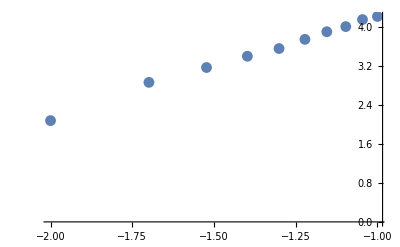

```mathematica
For[h=-1+0.3,h<-0.3,
h=h+0.1;
A=RegionPlot3D[x*x+y*y+z*z≤1,{x,-4,4},{y,-4,4},{z,-4,4},Mesh->None,PlotPoints->100,PlotStyle->Directive[Green,Opacity[0.8]],Boxed->False,BoundaryStyle->None,ImageSize->600,Axes->False,PlotRange->{-4,4}];
Needs["NDSolve`FEM`"];
mesh=ToElementMesh[DiscretizeGraphics[A],"MeshOrder"->1];
stressOperator[Y_,ν_]:={Inactive[Div][({{0,0,-((Y ν)/((1-2 ν) (1+ν)))},{0,0,0},{-(Y/(2 (1+ν))),0,0}}.Inactive[Grad][w[x,y,z],{x,y,z}]),{x,y,z}]+Inactive[Div][({{0,-((Y ν)/((1-2 ν) (1+ν))),0},{-(Y/(2 (1+ν))),0,0},{0,0,0}}.Inactive[Grad][v[x,y,z],{x,y,z}]),{x,y,z}]+Inactive[Div][({{-((Y (1-ν))/((1-2 ν) (1+ν))),0,0},{0,-(Y/(2 (1+ν))),0},{0,0,-(Y/(2 (1+ν)))}}.Inactive[Grad][u[x,y,z],{x,y,z}]),{x,y,z}],Inactive[Div][({{0,0,0},{0,0,-((Y ν)/((1-2 ν) (1+ν)))},{0,-(Y/(2 (1+ν))),0}}.Inactive[Grad][w[x,y,z],{x,y,z}]),{x,y,z}]+Inactive[Div][({{0,-(Y/(2 (1+ν))),0},{-((Y ν)/((1-2 ν) (1+ν))),0,0},{0,0,0}}.Inactive[Grad][u[x,y,z],{x,y,z}]),{x,y,z}]+Inactive[Div][({{-(Y/(2 (1+ν))),0,0},{0,-((Y (1-ν))/((1-2 ν) (1+ν))),0},{0,0,-(Y/(2 (1+ν)))}}.Inactive[Grad][v[x,y,z],{x,y,z}]),{x,y,z}],Inactive[Div][({{0,0,0},{0,0,-(Y/(2 (1+ν)))},{0,-((Y ν)/((1-2 ν) (1+ν))),0}}.Inactive[Grad][v[x,y,z],{x,y,z}]),{x,y,z}]+Inactive[Div][({{0,0,-(Y/(2 (1+ν)))},{0,0,0},{-((Y ν)/((1-2 ν) (1+ν))),0,0}}.Inactive[Grad][u[x,y,z],{x,y,z}]),{x,y,z}]+Inactive[Div][({{-(Y/(2 (1+ν))),0,0},{0,-(Y/(2 (1+ν))),0},{0,0,-((Y (1-ν))/((1-2 ν) (1+ν)))}}.Inactive[Grad][w[x,y,z],{x,y,z}]),{x,y,z}]};
Subscript[Γ,D]={DirichletCondition[{u[x,y,z]==0.,v[x,y,z]==0.,w[x,y,z]==0.},{z≥h}]};
Subscript[Γ2,D]={DirichletCondition[{u[x,y,z]==0.,v[x,y,z]==0.,w[x,y,z]==-z+h},{z<h}]};
E0=10^6;
V0=33/100;
mf=NDSolveValue[{stressOperator[E0,V0]=={0,0,0},Subscript[Γ,D],Subscript[Γ2,D]},{u,v,w},{x,y,z}∈mesh];
test[mf_,x_,y_,z_]:=(
{mf[[1]][x,y,z],mf[[2]][x,y,z],mf[[3]][x,y,z]}
);
uik=(Grad[test[mf,x,y,z],{x,y,z}]+
Transpose[Grad[test[mf,x,y,z],{x,y,z}]])/2.0;
ull2=Tr[uik]^2;
uik2=Total[Flatten[uik]*Flatten[uik]];
Fden=E0/(2*(1+V0))*(uik2+V0/(1-2V0)ull2);
F=NIntegrate[Fden,{x,y,z}∈Sphere[{0,0,0},1]];
AppendTo[hl,h+1];
AppendTo[Fl,F];
Print[h," ",F];
];
```

```mathematica
hl
```

{-0.99,-0.98,-0.97,-0.96,-0.95,-0.94,-0.93,-0.92,-0.91,-0.9}

```mathematica
hl+1
```

{0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}

```mathematica
hl=hl+1
```

{0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}

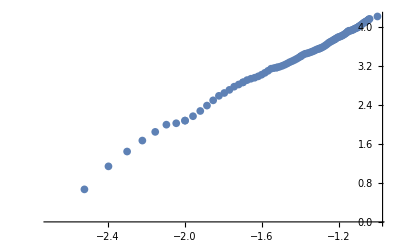

7.33154+2.96705 x

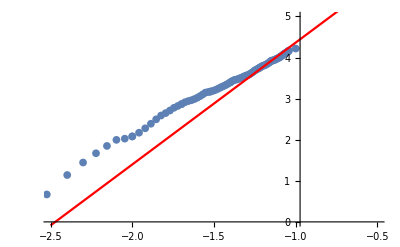

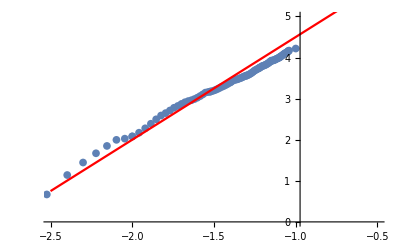

```mathematica
FIG1=ListPlot[Transpose[{Log10[hl],Log10[Fl]}]]
mp=Transpose[{Log10[hl],Log10[Fl]}];
mpf=Fit[Part[mp,75;;80],{1,x},x]
FIG2=Plot[mpf,{x,-2.5,0},PlotStyle->Red];
FIG3=Plot[7+2.5*x,{x,-2.5,0},PlotStyle->Red];
Show[{FIG1,FIG2},PlotRange->{{-2.5,-0.5},{0,5}}]
Show[{FIG1,FIG3},PlotRange->{{-2.5,-0.5},{0,5}}]
```

```mathematica
hl
```

{0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,-0.998,-0.997,-0.996,-0.995,-0.994,-0.993,-0.992,-0.991,-0.99,-0.989,-0.988,-0.987,-0.986,-0.985,-0.984,-0.983,-0.982,-0.981,-0.98,-0.979,-0.978,-0.977,-0.976,-0.975,-0.974,-0.973,-0.972,-0.971,-0.97,-0.969,-0.968,-0.967,-0.966,-0.965,-0.964,-0.963,-0.962,-0.961,-0.96,-0.959,-0.958,-0.957,-0.956,-0.955,-0.954,-0.953,-0.952,-0.951,-0.95,-0.949,-0.948,-0.947,-0.946,-0.945,-0.944,-0.943,-0.942,-0.941,-0.94,-0.939,-0.938,-0.937,-0.936,-0.935,-0.934,-0.933,-0.932,-0.931,-0.93,-0.929,-0.928,-0.927,-0.926,-0.925,-0.924,-0.923,-0.922,-0.921,-0.92,-0.919,-0.918,-0.917,-0.916,-0.915,-0.914,-0.913,-0.912,-0.911,-0.91,-0.909}

```mathematica
hl2={-0.998,-0.997,-0.996,-0.995,-0.994,-0.993,-0.992,-0.991,-0.99,-0.989,-0.988,-0.987,-0.986,-0.985,-0.984,-0.983,-0.982,-0.981,-0.98,-0.979,-0.978,-0.977,-0.976,-0.975,-0.974,-0.973,-0.972,-0.971,-0.97,-0.969,-0.968,-0.967,-0.966,-0.965,-0.964,-0.963,-0.962,-0.961,-0.96,-0.959,-0.958,-0.957,-0.956,-0.955,-0.954,-0.953,-0.952,-0.951,-0.95,-0.949,-0.948,-0.947,-0.946,-0.945,-0.944,-0.943,-0.942,-0.941,-0.94,-0.939,-0.938,-0.9369999999999999,-0.9359999999999999,-0.9349999999999999,-0.9339999999999999,-0.9329999999999999,-0.9319999999999999,-0.9309999999999999,-0.9299999999999999,-0.9289999999999999,-0.9279999999999999,-0.9269999999999999,-0.9259999999999999,-0.9249999999999999,-0.9239999999999999,-0.9229999999999999,-0.9219999999999999,-0.9209999999999999,-0.9199999999999999,-0.9189999999999999,-0.9179999999999999,-0.9169999999999999,-0.9159999999999999,-0.9149999999999999,-0.9139999999999999,-0.9129999999999999,-0.9119999999999999,-0.9109999999999999,-0.9099999999999999,-0.9089999999999999}
```

{-0.998,-0.997,-0.996,-0.995,-0.994,-0.993,-0.992,-0.991,-0.99,-0.989,-0.988,-0.987,-0.986,-0.985,-0.984,-0.983,-0.982,-0.981,-0.98,-0.979,-0.978,-0.977,-0.976,-0.975,-0.974,-0.973,-0.972,-0.971,-0.97,-0.969,-0.968,-0.967,-0.966,-0.965,-0.964,-0.963,-0.962,-0.961,-0.96,-0.959,-0.958,-0.957,-0.956,-0.955,-0.954,-0.953,-0.952,-0.951,-0.95,-0.949,-0.948,-0.947,-0.946,-0.945,-0.944,-0.943,-0.942,-0.941,-0.94,-0.939,-0.938,-0.937,-0.936,-0.935,-0.934,-0.933,-0.932,-0.931,-0.93,-0.929,-0.928,-0.927,-0.926,-0.925,-0.924,-0.923,-0.922,-0.921,-0.92,-0.919,-0.918,-0.917,-0.916,-0.915,-0.914,-0.913,-0.912,-0.911,-0.91,-0.909}

```mathematica
hl2=hl2+1
```

{0.002,0.003,0.004,0.005,0.006,0.007,0.008,0.009,0.01,0.011,0.012,0.013,0.014,0.015,0.016,0.017,0.018,0.019,0.02,0.021,0.022,0.023,0.024,0.025,0.026,0.027,0.028,0.029,0.03,0.031,0.032,0.033,0.034,0.035,0.036,0.037,0.038,0.039,0.04,0.041,0.042,0.043,0.044,0.045,0.046,0.047,0.048,0.049,0.05,0.051,0.052,0.053,0.054,0.055,0.056,0.057,0.058,0.059,0.06,0.061,0.062,0.063,0.064,0.065,0.066,0.067,0.068,0.069,0.07,0.071,0.072,0.073,0.074,0.075,0.076,0.077,0.078,0.079,0.08,0.081,0.082,0.083,0.084,0.085,0.086,0.087,0.088,0.089,0.09,0.091}

```mathematica
hl={0.010000000000000009,0.020000000000000018,0.030000000000000027,0.040000000000000036,0.050000000000000044,0.06000000000000005,0.07000000000000006,0.08000000000000007,0.09000000000000008,0.10000000000000009,0.0020000000000000018,0.0030000000000000027,0.0040000000000000036,0.0050000000000000044,0.006000000000000005,0.007000000000000006,0.008000000000000007,0.009000000000000008,0.010000000000000009,0.01100000000000001,0.01200000000000001,0.013000000000000012,0.014000000000000012,0.015000000000000013,0.016000000000000014,0.017000000000000015,0.018000000000000016,0.019000000000000017,0.020000000000000018,0.02100000000000002,0.02200000000000002,0.02300000000000002,0.02400000000000002,0.025000000000000022,0.026000000000000023,0.027000000000000024,0.028000000000000025,0.029000000000000026,0.030000000000000027,0.031000000000000028,0.03200000000000003,0.03300000000000003,0.03400000000000003,0.03500000000000003,0.03600000000000003,0.03700000000000003,0.038000000000000034,0.039000000000000035,0.040000000000000036,0.041000000000000036,0.04200000000000004,0.04300000000000004,0.04400000000000004,0.04500000000000004,0.04600000000000004,0.04700000000000004,0.04800000000000004,0.049000000000000044,0.050000000000000044,0.051000000000000045,0.052000000000000046,0.05300000000000005,0.05400000000000005,0.05500000000000005,0.05600000000000005,0.05700000000000005,0.05800000000000005,0.05900000000000005,0.06000000000000005,0.061000000000000054,0.062000000000000055,0.06300000000000006,0.06400000000000006,0.06500000000000006,0.06600000000000006,0.06700000000000006,0.06800000000000006,0.06900000000000006,0.07000000000000006,0.07100000000000006,0.07200000000000006,0.07300000000000006,0.07400000000000007,0.07500000000000007,0.07600000000000007,0.07700000000000007,0.07800000000000007,0.07900000000000007,0.08000000000000007,0.08100000000000007,0.08200000000000007,0.08300000000000007,0.08400000000000007,0.08500000000000008,0.08600000000000008,0.08700000000000008,0.08800000000000008,0.08900000000000008,0.09000000000000008,0.09100000000000008}
```

{0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.002,0.003,0.004,0.005,0.006,0.007,0.008,0.009,0.01,0.011,0.012,0.013,0.014,0.015,0.016,0.017,0.018,0.019,0.02,0.021,0.022,0.023,0.024,0.025,0.026,0.027,0.028,0.029,0.03,0.031,0.032,0.033,0.034,0.035,0.036,0.037,0.038,0.039,0.04,0.041,0.042,0.043,0.044,0.045,0.046,0.047,0.048,0.049,0.05,0.051,0.052,0.053,0.054,0.055,0.056,0.057,0.058,0.059,0.06,0.061,0.062,0.063,0.064,0.065,0.066,0.067,0.068,0.069,0.07,0.071,0.072,0.073,0.074,0.075,0.076,0.077,0.078,0.079,0.08,0.081,0.082,0.083,0.084,0.085,0.086,0.087,0.088,0.089,0.09,0.091}